```mathematica
(*firstorder RMS approximation model
See P-25:Inter-Grey-Level Response Times of a Liquid Crystal Display*)
(* Variables *)
ContrastRatio := 200.0;
Transmission := 0.9;
PixelSpeed  :=0.0029;
Persistence :=0.006;
PersistenceDelay:=0.004;
FrameRate = 100;
PWMFrequency = 500;
Brightness = 0.5;
(* Definitions *)
T[V_]:=(1-Tanh[2V-4])/2(*Roungh Transmission vs internal voltage fit*)
V[T_]:=1/2 (4+ArcTanh[1-2 T]) (*Inverse of the above*)
Vbright = V[Transmission];
Vdark = V[Transmission/ContrastRatio];
PersistenceDutyCycle = Persistence*FrameRate;

(*Input Signal*)
Signal[t_]:=UnitBox[FrameRate t-0.5]+UnitBox[FrameRate t-2.5]+1/2 UnitBox[FrameRate t-3.5]

(* Pixel Response, RMS model*)
StepResponse[t_,PixelSpeed_]:=Piecewise[{{√(1-ⅇ^(-t/PixelSpeed)), 0<t<5PixelSpeed}, {0, True}}](*Pixel Response, Windowed to 5 Tau*)
ImpulseResponse[t_,PixelSpeed_]=Evaluate@D[StepResponse[t,PixelSpeed],t];

(*Cacluating Output *)
Vextern[t_]:=V[Transmission*Signal[t]+Transmission/ContrastRatio] (*no overdrive*)
Vpixel[t_]:=Evaluate@NIntegrate[ImpulseResponse[s,PixelSpeed]*Vextern[t-s],{s,0,0,5*PixelSpeed},MaxRecursion->4]//Quiet (*convolution*)
Tpixel[t_]:= T[Vpixel[t]]
```

```mathematica
(*Persistence and PWM simulation*)
DutyWave[t_,Duty_]:=Piecewise[{{SquareWave[{1,0},t-0.5]*SquareWave[{1,0},t-Duty], 0<=Duty<=0.5}, {Max[SquareWave[{1,0},t-0.5],SquareWave[{1,0},t-Duty]], 0.5<Duty<1}, {1, True}}]
Plot[DutyWave[t,0.75],{t,-1,1},AxesOrigin->{0,0},PlotRange->Full,Filling->True];
Plot[DutyWave[FrameRate (t-PersistenceDelay),PersistenceDutyCycle],{t,0,2/FrameRate},AxesOrigin->{0,0},PlotRange->Full,Filling->True];
```

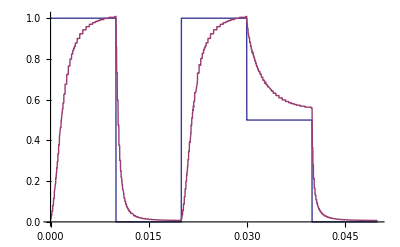

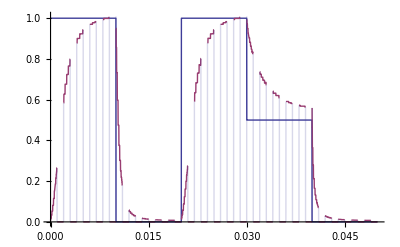

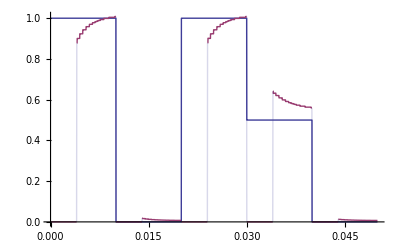

```mathematica
(*Plots*)
(*Full persistence*)
Plot[{Signal[t],1/Transmission Tpixel[t]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis}]//Quiet
(*Full persistence + PWM*)
Plot[{Signal[t],1/Transmission Tpixel[t]*DutyWave[ PWMFrequency t,Brightness]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis}]//Quiet
(*Low Persistence*)
Plot[{Signal[t],1/Transmission Tpixel[t]*DutyWave[FrameRate (t-PersistenceDelay),PersistenceDutyCycle]},{t,0,5/FrameRate},AxesOrigin->{0,0},Filling->{False,Axis}]//Quiet
```

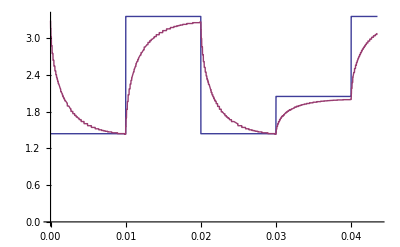

```mathematica
Plot[{Vextern[t],Vpixel[t]},{t,0,15*PixelSpeed},PlotRange->Full,AxesOrigin->{0,0}]//Quiet
```